## Previous functions

### Gram Matrix Generation

```mathematica
CoeffNum[d_,Nt_,J_]:=(Nt+1)^2*ResourceFunction["NineJSymbol"][{{(Nt-d)/2,d/2,Nt/2},{d/2,(Nt-d)/2,Nt/2},{Nt/2,Nt/2,J}}];
Coeff[n_,m_,Nt_,J_]:=Module[
{d,factor1,zmin,zmax,factor2},
d=Abs[m-n];
factor1 = ((Nt-d)!*d!*(Nt-J)!)/(Nt!*Nt!);
zmin=Max[{d-J,0}];
zmax=Min[{Nt-J,d}];
factor2=Total[Table[(-1)^z*((Nt-z)!*(J+z)!)/((Nt-J-z)!*(d-z)!*(J-d+z)!*z!),{z,zmin,zmax}]];
factor1*factor2
]

GMatrix[Nt_,J_]:=Table[Coeff[a-1,b-1,Nt,J],{a,Nt},{b,Nt}];
SMatrix[Nt_,J_]:=MatrixPower[N[GMatrix[Nt,J]],1/2];
```

### Analytical SRM

```mathematica
(*DIMENSIONAL FACTOR*)
Dsym[Nt_,d_]:=Binomial[d+Nt-1,d-1];
Sl[Nt_,l_,d_]:=(Nt-2*l+1)/(Nt-l+1)*Binomial[d+l-2,d-2]*Binomial[d+Nt-l-1,d-1];
Dim[Nt_,J_,d_]:=Sl[Nt,Nt/2-J,d]/Dsym[Nt,d]^2;

(*FORMULA*)
Vap[Ntotal_,J_,k_]:=Sum[Coeff[0,r,Ntotal,J]*Exp[(2*Pi*I)/Ntotal*(k+1/2*Mod[Ntotal+J,2])*r],{r,0,Ntotal-1}];
SRMAnalyticalPre[Ntotal_,d_]:=1/Ntotal^2*Sum[Dim[Ntotal,J,d]*(Sum[Sqrt[Vap[Ntotal,J,k]],{k,0,Ntotal-1}])^2,{J,0,Ntotal}];
SRMAnalytical[Ntotal_,d_]:=Re[N[SRMAnalyticalPre[Ntotal,d]]];
```

```mathematica
SRMAnalytical[20,2]
SRMAnalytical[20,3]
SRMAnalytical[20,4]
SRMAnalytical[20,8]
```

0.75058

-0.138681

0.113966

0.000760389

```mathematica
Dim[n,j,2]//FullSimplify
```

(1+2 j)/(1+n)^2

### Plots

```mathematica
Prov[Ntotal_,d_]:=Table[Re[N[1/Ntotal^2*Dim[Ntotal,J,d]*(Sum[Sqrt[Vap[Ntotal,J,k]],{k,0,Ntotal-1}])^2]],{J,0,Ntotal}];
```

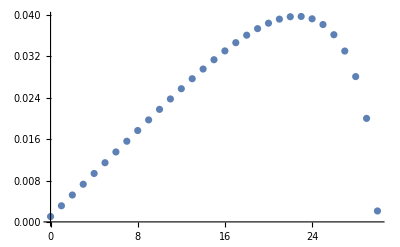

```mathematica
Nt=30;
data=Transpose[{Range[0,Nt],Prov[Nt,2]}];
ListPlot[data]
```

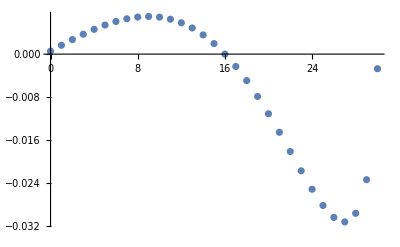

{0.000552502,0.00164544,0.00270211,0.00369821,0.00460917,0.00541021,0.00607629,0.00658216,0.00690254,0.0070123,0.00688673,0.00650204,0.00583581,0.00486772,0.00358039,0.00196047}

0.0748241

```mathematica
Nt=30;
data=Transpose[{Range[0,Nt],Prov[Nt,3]}];
ListPlot[data]

yvals=Select[Prov[Nt,3],Positive]
Total[yvals]
```

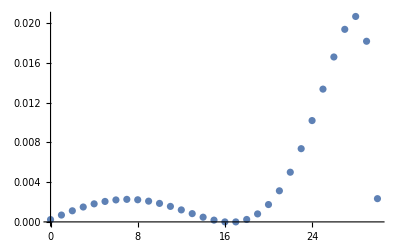

```mathematica
Nt=30;
data=Transpose[{Range[0,Nt],Prov[Nt,4]}];
ListPlot[data]
```

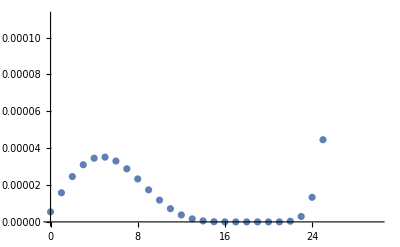

```mathematica
Nt=30;
data=Transpose[{Range[0,Nt],Prov[Nt,8]}];
ListPlot[data]
```